===============================================================================

Dalam menjawab soal-soal berikut, saya mengasumsikan bahwa orang awam adalah orang-orang dengan kemampuan matematika yang cukup, yakni setidaknya memiliki pemahaman atas fungsi, deret, dan integral serta berkeinginan untuk mempelajari atau menerapkan Wolfram Mathematica.

Pekerjaan ini merupakan lanjutan dari yang sebelumnya, yakni tugas pertama, maka penjelasan tidak akan membahas secara detail seperti sebelumnya.

===============================================================================
===============================================================================

1. 
Barisan x_n didefinisikan dengan x_n=1/2(1-(-1)^n), n ∈ ℕ
Barisan s_n didefinisikan dengan s_n=x_1+x_2+...+x_n untuk n ∈ ℕ.
Apakah barisan s_n/n konvergen? Jika ya, tentukan limitnya.

------------------------------------------------------------------------------------------------------------------------------------------

Pertama-tama kita definisikan x_n

```mathematica
x[n_]:=1/2(1 - (-1)^n)
```

Selanjutnya kita definisikan s_n sebagai penjumlahan dari 1 hingga n, maka kita gunakan {i, 1, n} di dalam Sum

```mathematica
s[n_]:=Sum[
x[i],{i,1,n}
]
```

Untuk mengetahui apakah s_n/n konvergen, dapat digunakan 2 cara, yaitu dengan melakukan uji deret atau dengan menggunakan plotting.
Agar mudah dan karena kita menggunakan Mathematica, mari kita buat plottingnya saja.

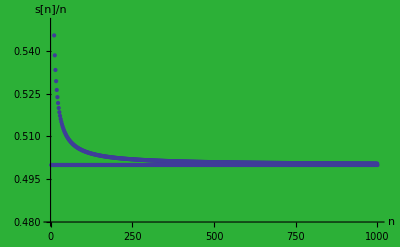

```mathematica
ListPlot[
Table[
s[n]/n,{n, 1, 1000}
],
PlotRange->{0.48,0.55},
AxesLabel->{"n","s[n]/n"},
Background->RGBColor[44/255,176/255,55/255]
]
```

Dapat terlihat jelas bahwa semakin n menuju ∞, maka s_n/n akan menuju 0.5.
Apabila kita hitung menggunakan fungsi Limit:

```mathematica
Limit[s[n]/n,n->∞]
```

1/2

Maka, s_n/n konvergen dan limitnya bernilai 1/2.

Maka dengan ini, soal nomor 1 telah terjawab.

===============================================================================
===============================================================================

2.
Carilah approksimasi dari f(x)=ⅇ^(-x^2) pada batas interval [1,3] dengan Monte Carlo.
Namun dalam pencarian aproksimasi tersebut, gunakan Monte Carlo dengan pembuatan program Monte Carlo sehingga pada pencarian aproksimasi tersebut hanya dengan memanggil program Monte carlo yang sudah kita buat.

------------------------------------------------------------------------------------------------------------------------------------------

Pertama-tama, agar mendapat ide mengenai apa yang dikerjakan, mari buat gambar dari fungsi f(x)=ⅇ^(-x^2) pada interval [1,3]

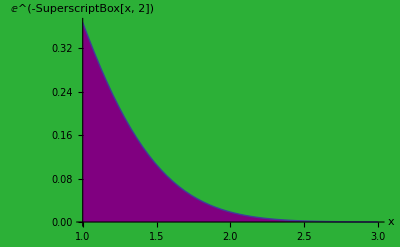

```mathematica
Plot[
ⅇ^(-x^2),{x,1,3},
Filling->Axis,
FillingStyle->Purple,
AxesLabel->{"x","ⅇ^(-SuperscriptBox[x, 2])"},
Background->RGBColor[44/255,176/255,55/255]
]
```

Perhatikan bahwa fungsi tersebut memiliki batas atas (saat memasukkan x=1) yaitu ⅇ^(-1^2)=ⅇ^-1
dan fungsi tersebut memiliki batas bawah (saat memasukkan x=3) yaitu ⅇ^(-3^2)=ⅇ^-9

Maka kita akan dasarkan fungsi yang dibuat dengan membuat persebaran titik di X pada [1,3]
dan persebaran titik di ⅇ^(-x^2) atau Y pada [ⅇ^-9,ⅇ^-1]

Sebelum kita mendefinisikan fungsi tersebut, kita perlu mengidentifikasi parameter-parameter yang perlu digunakan.
Paramater-parameter tersebut yaitu:
1. RandomX (memetakan titik-titik acak di X)	-> RndX
2. RandomY (memetakan titik-titik acak di Y)	-> RndY
3. Plot							-> plt, ListTitik
4. Titik yang berada dalam area yang diarsir	-> Titik
5. Luas Approksimasi				-> LuasAppr
6. Luas Eksak atau Luas Sebenarnya		-> LuasAsli
7. Galat metode Monte Carlo			-> Galat
Ketujuh parameter ini akan masuk dalam fungsi yang didefinisikan.

Kita definisikan sebuah fungsi bernama MonteCarlo di mana MonteCarlo akan menerima input n dimana n adalah jumlah titik yang disebar.

```mathematica
MonteCarlo[n_]:=
Module[
{RndX, RndY, plt, ListTitik, Titik,LuasAppr,LuasAsli,Galat},

RndX=Table[RandomReal[{1,3}],{x,1,n}];
RndY=Table[RandomReal[{ⅇ^-9,ⅇ^-1}],{x,1,n}];

plt = Plot[
ⅇ^(-x^2),{x,1,3},
Filling->Axis,
FillingStyle->Purple,
PlotStyle->{Red,Thickness[0.01]},
Background ->RGBColor[44/255,176/255,55/255],
PlotLegends->SwatchLegend["Expressions",
LegendFunction->(Framed[#,Background->Gray]&)]
];
ListTitik=ListPlot[
Table[
{RndX[[i]],RndY[[i]]},{i,n}
],
Background->RGBColor[44/255,176/255,55/255]
];

Titik=0;
For[
i=1,i≤n,i++,
If[
RndY[[i]]≤ⅇ^(-(RndX[[i]])^2),Titik=Titik+ 1
]
];

LuasAppr=N[Titik/n*2 ⅇ^-1];

LuasAsli=N[∫_1^3 ⅇ^(-x^2)ⅆx];

Galat=Abs[LuasAsli-LuasAppr];

Print[
"Jumlah titik yang disebar: ", n, " titik"
];
Print[
"Jumlah titik yang berada dalam daerah arsiran: ",Titik," titik"
];
Print[
"Luas arsiran menggunakan metode Monte Carlo: ", LuasAppr, " satuan luas"
];
Print[
"Luas arsiran yang sebenarnya: ", LuasAsli, " satuan luas"
];
Print[
"
Galat metode Monte Carlo: ",Galat, " satuan luas"
];


Show[
plt,ListTitik
]
]
```

Dengan ini, kita telah mendefinisikan fungsi Monte Carlo untuk menjawab soal ini.

Mari kita panggil fungsi ini dengan misal 3000 titik.

Jumlah titik yang disebar: 3000 titik

Jumlah titik yang berada dalam daerah arsiran: 568 titik

Luas arsiran menggunakan metode Monte Carlo: 0.139304 satuan luas

Luas arsiran yang sebenarnya: 0.139383 satuan luas

Galat metode Monte Carlo: 0.0000795337 satuan luas

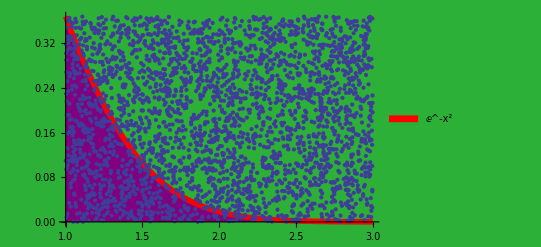

```mathematica
MonteCarlo[3000]
```

Maka dengan ini, nomor 2 telah terjawab

===============================================================================
===============================================================================

3.
Carilah gambar fungsi Archimedean Spirals dari bentuk r=θ^(1/n). Dengan bentuk seperti berikut:

------------------------------------------------------------------------------------------------------------------------------------------

Mengasumsikan maksud dari soal adalah menggambarkan kedua plot tersebut, saya akan jawab lebih lanjut dengan membuat manipulasi perubahan pangkat pada r yaitu dengan mengubah nilai n.

Pertama kita definisikan r.

```mathematica
r[n_]:=θ^(1/n)
```

Untuk menggambar plot sesuai soal, kita gunakan fungsi bernama PolarPlot.

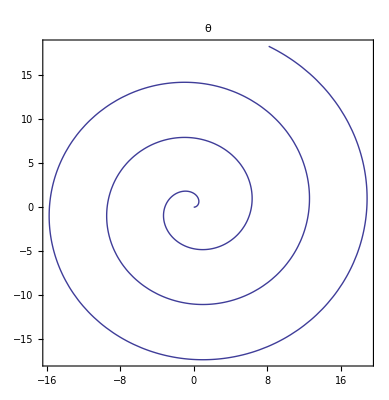
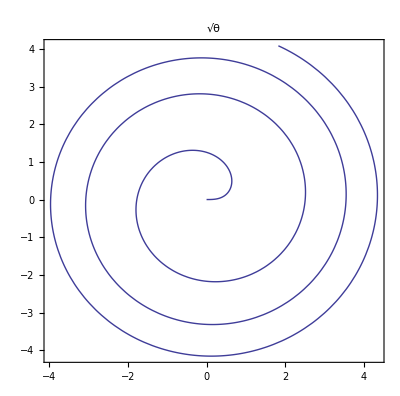

```mathematica
{PolarPlot[
r[1],{θ,0,20},
Frame->True,
Background->RGBColor[1,1,1],
PlotLabel->Style[Framed[r[1],Background->LightCyan]]
],
PolarPlot[
r[2],{θ,0,20},
Frame->True,
Background->RGBColor[1,1,1],
PlotLabel->Style[Framed[r[2],Background->LightCyan]]
]}
```

Selanjutnya mari kita melangkah lebih lanjut dengan membuat manipulasi perubahan pangkat pada r yaitu dengan mengubah nilai n.

Kita definisikan sebuah fungsi ArchimedeanPlot yang memanipulasi input n dari interval sesuai yang diinginkan.

```mathematica
ArchimedeanPlot[i1_, i2_]:=Manipulate[
PolarPlot[
r[n],{θ,0,20},
Frame->True,
PlotStyle->Thick,
ColorFunction->Function[{x,y,θ},Hue[θ/(2Pi)]],
ColorFunctionScaling->False,
Background->RGBColor[44/255,176/255,55/255],
PlotLabel->Style[Framed[r[n],Background->LightCyan]]
],
{n,i1,i2}
]
```

Melakukan ini menarik karena kita dapat melihat proses yang terjadi, misal kita ambil interval [1,2] seperti soal

```mathematica
ArchimedeanPlot[1,2]
```

sehingga kita dapat melihat perubahan bertahap yang terjadi pada plot fungsi ini.

Maka dengan ini, soal nomor 3 telah terjawab.